# Characteristics of Eigen(new)

## Program

```mathematica
Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/List_operations.txt"]
```

```mathematica
Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Matrix_operations.txt"]
```

```mathematica
Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Chemicalform_operations.txt"]
```

```mathematica
(*Get["/Users/amanokou/gitsrc/MATH_SCRIPT/SCRIPTS/Matrix_operations.txt"]*)
```

## 基本的性質

```mathematica
A={{1,2,5},{2,3,6},{9,3,1}}
```

{{1,2,5},{2,3,6},{9,3,1}}

```mathematica
v=Eigenvalues[A]//N
```

{10.5457,-5.80694,0.261275}

```mathematica
u=Eigenvectors[A]//N
```

{{0.730993,0.98891,1.},{-0.572576,-0.551252,1.},{0.856735,-2.81645,1.}}

```mathematica
A.u[[1]]
```

{7.70881,10.4287,10.5457}

```mathematica
v[[1]] u[[1]]
```

{7.70881,10.4287,10.5457}

```mathematica
A.Normalize[u[[1]]]
```

{4.86354,6.57954,6.65333}

```mathematica
v[[1]] Normalize[u[[1]]]
```

{4.86354,6.57954,6.65333}

## 対称行列の固有値・固有ベクトルの性質

1. 一般的に固有値はノルムの大きい固有値順に求まる(ソートされる)。

2. eigen valuesは行列を並べ替えても保たれるか:
=> 行列の行と列を同じオーダーで入れ替えると保たれる。

3. eigen valuesはzeroのインサートにより保たれるか:
=> 行列に対する同じオーダーでの挿入により保たれる。

4. eigen vectorの要素の絶対値の大きさ順に行列を並べ替えた後のeigen vectorは、大きさの順位を保っているか:
=> 保たれている。

5. PCA(Eigenvectors(mat)) == PCA(Eigenvectors(matReOrder[mat])) <= 場合によって(reorder)はTrue
    PCA(mat) == PCA(matReOrder[mat]) <= NotTrue
    Eigenvectors(mat) == Eigenvectors(matReOrder[mat]) <= NotTrue

```mathematica
(SA=toSymmetric[A])//MatrixForm
```

(30 | 38 | 20
38 | 49 | 33
20 | 33 | 91)

```mathematica
(SAr=matReOrder[SA,{2,1,3}])//MatrixForm
```

(49 | 38 | 33
38 | 30 | 20
33 | 20 | 91)

```mathematica
Eigenvalues[SA]//N
```

{123.744,46.2116,0.0447678}

```mathematica
Eigenvalues[SAr]//N
```

{123.744,46.2116,0.0447678}

```mathematica
Eigenvectors[SA]//N
```

{{0.494158,0.692741,1.},{-0.804612,-0.86958,1.},{12.2364,-10.1722,1.}}

```mathematica
Eigenvectors[SAr]//N
```

{{0.692741,0.494158,1.},{-0.86958,-0.804612,1.},{-10.1722,12.2364,1.}}

```mathematica
PrincipalComponents[Eigenvectors[SA]//N]
```

{{5.31461,1.01646,0.},{5.33613,-1.01509,0.},{-10.6507,-0.00136869,0.}}

```mathematica
PrincipalComponents[Eigenvectors[SAr]//N]
```

{{5.31461,1.01646,0.},{5.33613,-1.01509,0.},{-10.6507,-0.00136869,0.}}

```mathematica
RS=randomSymmetricMat[7,{1,7}]
```

{{137,133,104,114,131,101,80},{133,155,98,109,145,103,95},{104,98,98,101,105,92,76},{114,109,101,136,126,92,88},{131,145,105,126,158,108,106},{101,103,92,92,108,96,88},{80,95,76,88,106,88,105}}

```mathematica
RSr=matReOrder[RS,{6,4,2,7,5,3,1}]
```

{{96,92,103,88,108,92,101},{92,136,109,88,126,101,114},{103,109,155,95,145,98,133},{88,88,95,105,106,76,80},{108,126,145,106,158,105,131},{92,101,98,76,105,98,104},{101,114,133,80,131,104,137}}

```mathematica
RSva=Eigenvalues[RS]//N
```

{763.569,44.6423,39.8187,24.8129,6.94806,4.52926,0.67985}

```mathematica
RSrva=Eigenvalues[RSr]//N
```

{763.569,44.6423,39.8187,24.8129,6.94806,4.52926,0.67985}

```mathematica
RSpc=PrincipalComponents[Eigenvectors[RS//N]]
```

{{0.,0.,0.,0.,0.92582,0.,0.},{-0.79004,-0.0391429,-0.391516,0.114018,-0.154303,-0.203354,0.},{0.0526992,-0.592778,0.581899,0.0317543,-0.154303,-0.37357,0.},{0.198124,-0.452018,-0.313184,-0.076376,-0.154303,0.697024,0.},{0.503197,0.250232,-0.293604,0.590678,-0.154303,-0.287064,0.},{-0.181927,0.544547,0.552531,0.12461,-0.154303,0.427652,0.},{0.217948,0.289161,-0.136127,-0.784685,-0.154303,-0.260687,0.}}

```mathematica
RSrpc=PrincipalComponents[Eigenvectors[RSr//N]]
```

{{0.,2.14964×10^-16,0.92582,0.,0.,0.,0.},{-0.194097,-0.442616,-0.154303,0.638097,-0.438681,-0.0119247,0.},{0.416041,0.523858,-0.154303,-0.0516195,-0.420151,0.454559,0.},{0.316101,-0.575624,-0.154303,-0.616495,-0.072367,-0.129489,0.},{-0.806451,0.180481,-0.154303,-0.350323,0.0406896,0.161291,0.},{0.17249,-0.0843784,-0.154303,0.276908,0.782623,0.327541,0.},{0.095916,0.39828,-0.154303,0.103433,0.107887,-0.801978,0.}}

```mathematica
RSvecs=Map[Normalize,Eigenvectors[RS]//N]
```

{{0.400486,0.420505,0.334195,0.381328,0.439726,0.33669,0.314595},{-0.461456,-0.445992,0.0877484,0.191809,-0.0579352,0.222703,0.700504},{-0.173156,0.469241,-0.369896,-0.632087,0.212858,0.0440035,0.407712},{-0.240916,0.0905425,-0.464397,0.520233,0.421663,-0.519078,0.0145658},{0.202854,0.380202,-0.243492,0.300164,-0.75118,-0.111024,0.297176},{0.677603,-0.498434,-0.468752,-0.0978945,0.124999,0.0274344,0.21617},{0.195833,-0.053783,0.499108,-0.218953,0.0167723,-0.743361,0.32991}}

```mathematica
RSrvecs=Map[Normalize,Eigenvectors[RSr]//N]
```

{{0.33669,0.381328,0.420505,0.314595,0.439726,0.334195,0.400486},{-0.222703,-0.191809,0.445992,-0.700504,0.0579352,-0.0877484,0.461456},{-0.0440035,0.632087,-0.469241,-0.407712,-0.212858,0.369896,0.173156},{0.519078,-0.520233,-0.0905425,-0.0145658,-0.421663,0.464397,0.240916},{-0.111024,0.300164,0.380202,0.297176,-0.75118,-0.243492,0.202854},{0.0274344,-0.0978945,-0.498434,0.21617,0.124999,-0.468752,0.677603},{-0.743361,-0.218953,-0.053783,0.32991,0.0167723,0.499108,0.195833}}

```mathematica
RS.RSvecs[[1]]
```

{305.799,321.085,255.181,291.17,335.761,257.086,240.215}

```mathematica
RSva[[1]] RSvecs[[1]]
```

{305.799,321.085,255.181,291.17,335.761,257.086,240.215}

```mathematica
Outer[EuclideanDistance,RSvecs,RSvecs,1]
```

{{0.,1.41421,1.41421,1.41421,1.41421,1.41421,1.41421},{1.41421,0.,1.41421,1.41421,1.41421,1.41421,1.41421},{1.41421,1.41421,0.,1.41421,1.41421,1.41421,1.41421},{1.41421,1.41421,1.41421,0.,1.41421,1.41421,1.41421},{1.41421,1.41421,1.41421,1.41421,0.,1.41421,1.41421},{1.41421,1.41421,1.41421,1.41421,1.41421,0.,1.41421},{1.41421,1.41421,1.41421,1.41421,1.41421,1.41421,0.}}

```mathematica
Outer[EuclideanDistance,RSrvecs,RSrvecs,1]
```

{{0.,1.41421,1.41421,1.41421,1.41421,1.41421,1.41421},{1.41421,0.,1.41421,1.41421,1.41421,1.41421,1.41421},{1.41421,1.41421,0.,1.41421,1.41421,1.41421,1.41421},{1.41421,1.41421,1.41421,0.,1.41421,1.41421,1.41421},{1.41421,1.41421,1.41421,1.41421,0.,1.41421,1.41421},{1.41421,1.41421,1.41421,1.41421,1.41421,0.,1.41421},{1.41421,1.41421,1.41421,1.41421,1.41421,1.41421,0.}}

## Matrix types (特別な行列のタイプ)

```mathematica
??Eigenvectors
```

RowBox[{"Eigenvectors", "[", StyleBox["m", "TI"], "]"}] 正方行列 StyleBox[RowBox[{"m", " "}], "TI"]の固有ベクトルのリストを与える．
RowBox[{"Eigenvectors", "[", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], "]"}] StyleBox[RowBox[{"a", " "}], "TI"]についての StyleBox[RowBox[{"m", " "}], "TI"]の一般化された固有ベクトルを与える．
RowBox[{"Eigenvectors", "[", RowBox[{StyleBox["m", "TI"], ",", StyleBox["k", "TI"]}], "]"}] StyleBox[RowBox[{"m", " "}], "TI"]の最初のStyleBox[RowBox[{" ", "k", " "}], "TI"]個の固有ベクトルを与える．
RowBox[{"Eigenvectors", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], ",", StyleBox["k", "TI"]}], "]"}] 最初の StyleBox[RowBox[{"k", " "}], "TI"]個の一般化された固有ベクトルを与える．

Attributes[Eigenvectors]={Protected}
 
Options[Eigenvectors]={Cubics→False,Method→Automatic,Quartics→False,ZeroTest→Automatic}

Column vector correspond to each vector of original matrix.

Row vector correspond to 1st property of all vector of original matrix.

```mathematica
??IncidenceMatrix
```

RowBox[{"IncidenceMatrix", "[", StyleBox["g", "TI"], "]"}] gives the vertex-edge incidence matrix of the graph StyleBox["g", "TI"].
RowBox[{"IncidenceMatrix", "[", RowBox[{"{", RowBox[{RowBox[{StyleBox["v", "TI"], "→", StyleBox["w", "TI"]}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] uses rules RowBox[{StyleBox["v", "TI"], "→", StyleBox["w", "TI"]}] to specify the graph StyleBox["g", "TI"].

Attributes[IncidenceMatrix]={Protected}

```mathematica
??KirchhoffMatrix (*Laplacian matrix*)
```

RowBox[{"KirchhoffMatrix", "[", StyleBox["g", "TI"], "]"}] gives the Kirchhoff matrix of the graph StyleBox["g", "TI"].
RowBox[{"KirchhoffMatrix", "[", RowBox[{"{", RowBox[{RowBox[{StyleBox["v", "TI"], "→", StyleBox["w", "TI"]}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] uses rules RowBox[{StyleBox["v", "TI"], "→", StyleBox["w", "TI"]}] to specify the graph StyleBox["g", "TI"].

Attributes[KirchhoffMatrix]={Protected,ReadProtected}

Information::nomatch: No symbol matching (*Laplacian found.

Information::nomatch: No symbol matching matrix*) found.

## 密行列

## 密行列

### Eigenvalues

```mathematica
(m=Table[RandomReal[],{6},{6}])//TableForm
```

0.046276 | 0.0718178 | 0.593693 | 0.0677938 | 0.360611 | 0.627972
0.0684557 | 0.910455 | 0.840521 | 0.0390658 | 0.749585 | 0.157494
0.389655 | 0.769601 | 0.970059 | 0.104432 | 0.600158 | 0.544781
0.087122 | 0.13173 | 0.124536 | 0.149748 | 0.942151 | 0.301013
0.67842 | 0.111246 | 0.855427 | 0.249406 | 0.730884 | 0.120885
0.407673 | 0.284456 | 0.0169892 | 0.464352 | 0.0307249 | 0.207402

```mathematica
eval["orig"]=Eigenvalues[m]
```

{2.5514+0. ⅈ,0.745409+0. ⅈ,-0.676554+0. ⅈ,0.275266+0.475851 ⅈ,0.275266-0.475851 ⅈ,-0.155959+0. ⅈ}

```mathematica
Eigenvalues[2 m]
```

{5.10279+0. ⅈ,1.49082+0. ⅈ,-1.35311+0. ⅈ,0.550532+0.951701 ⅈ,0.550532-0.951701 ⅈ,-0.311918+0. ⅈ}

```mathematica
ro={2,3,5,1,6,4}
```

{2,3,5,1,6,4}

```mathematica
Eigenvalues[matRowReOrder[m,ro]]
```

{2.32708+0. ⅈ,0.594701+0. ⅈ,-0.584292+0. ⅈ,-0.257974+0.457938 ⅈ,-0.257974-0.457938 ⅈ,0.271477+0. ⅈ}

```mathematica
Eigenvalues[matColReOrder[m,ro]]
```

{2.55495+0. ⅈ,0.619736+0. ⅈ,-0.360278+0.458285 ⅈ,-0.360278-0.458285 ⅈ,-0.496346+0. ⅈ,0.227069+0. ⅈ}

```mathematica
eval["reo"]=Eigenvalues[matReOrder[m,ro]]
```

{2.5514+0. ⅈ,0.745409+0. ⅈ,-0.676554+0. ⅈ,0.275266+0.475851 ⅈ,0.275266-0.475851 ⅈ,-0.155959+0. ⅈ}

```mathematica
Eigenvalues[zeroInsert[m,2,3]]
```

{2.5514+0. ⅈ,0.745409+0. ⅈ,-0.676554+0. ⅈ,0.275266+0.475851 ⅈ,0.275266-0.475851 ⅈ,-0.155959+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

### Eigenvectors

```mathematica
evec["orig"]=Eigenvectors[m]
```

{{-0.268368+0. ⅈ,-0.536512+0. ⅈ,-0.576934+0. ⅈ,-0.268452+0. ⅈ,-0.452287+0. ⅈ,-0.175075+0. ⅈ},{0.21369+0. ⅈ,-0.593705+0. ⅈ,-0.290894+0. ⅈ,0.542746+0. ⅈ,0.34046+0. ⅈ,0.326718+0. ⅈ},{-0.518685+0. ⅈ,-0.141863+0. ⅈ,-0.0910241+0. ⅈ,-0.521111+0. ⅈ,0.36185+0. ⅈ,0.547781+0. ⅈ},{-0.329407-0.040946 ⅈ,0.287806-0.104131 ⅈ,-0.24617-0.0779549 ⅈ,0.564915+0. ⅈ,0.100582+0.454532 ⅈ,-0.00801874-0.439947 ⅈ},{-0.329407+0.040946 ⅈ,0.287806+0.104131 ⅈ,-0.24617+0.0779549 ⅈ,0.564915+0. ⅈ,0.100582-0.454532 ⅈ,-0.00801874+0.439947 ⅈ},{0.509499+0. ⅈ,0.179267+0. ⅈ,-0.403602+0. ⅈ,-0.698812+0. ⅈ,0.14804+0. ⅈ,0.187418+0. ⅈ}}

```mathematica
evec["reo"]=Eigenvectors[matReOrder[m,ro]]
```

{{-0.536512+0. ⅈ,-0.576934+0. ⅈ,-0.452287+0. ⅈ,-0.268368+0. ⅈ,-0.175075+0. ⅈ,-0.268452+0. ⅈ},{-0.593705+0. ⅈ,-0.290894+0. ⅈ,0.34046+0. ⅈ,0.21369+0. ⅈ,0.326718+0. ⅈ,0.542746+0. ⅈ},{-0.141863+0. ⅈ,-0.0910241+0. ⅈ,0.36185+0. ⅈ,-0.518685+0. ⅈ,0.547781+0. ⅈ,-0.521111+0. ⅈ},{0.287806-0.104131 ⅈ,-0.24617-0.0779549 ⅈ,0.100582+0.454532 ⅈ,-0.329407-0.040946 ⅈ,-0.00801874-0.439947 ⅈ,0.564915+0. ⅈ},{0.287806+0.104131 ⅈ,-0.24617+0.0779549 ⅈ,0.100582-0.454532 ⅈ,-0.329407+0.040946 ⅈ,-0.00801874+0.439947 ⅈ,0.564915+0. ⅈ},{-0.179267+0. ⅈ,0.403602+0. ⅈ,-0.14804+0. ⅈ,-0.509499+0. ⅈ,-0.187418+0. ⅈ,0.698812+0. ⅈ}}

PCA

```mathematica
evecP["orig"]=Eigenvectors[PrincipalComponents[m]]
```

{{0.0151844+0.349361 ⅈ,-0.386937-0.31831 ⅈ,-0.104804-0.110453 ⅈ,-0.292203+0.183831 ⅈ,0.0861238-0.104429 ⅈ,0.682636+0. ⅈ},{0.0151844-0.349361 ⅈ,-0.386937+0.31831 ⅈ,-0.104804+0.110453 ⅈ,-0.292203-0.183831 ⅈ,0.0861238+0.104429 ⅈ,0.682636+0. ⅈ},{-0.153477+0.206767 ⅈ,0.178194+0.143807 ⅈ,-0.382534+0.127823 ⅈ,0.202019-0.372562 ⅈ,-0.429858-0.105834 ⅈ,0.585657+0. ⅈ},{-0.153477-0.206767 ⅈ,0.178194-0.143807 ⅈ,-0.382534-0.127823 ⅈ,0.202019+0.372562 ⅈ,-0.429858+0.105834 ⅈ,0.585657+0. ⅈ},{0.0743941+0. ⅈ,-0.148921+0. ⅈ,0.410132+0. ⅈ,0.0990526+0. ⅈ,-0.808854+0. ⅈ,0.374197+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}}

```mathematica
evec["reo"]=Eigenvectors[PrincipalComponents[matReOrder[m,ro]]]
```

{{-0.0912247+0. ⅈ,-0.135465+0. ⅈ,0.860679+0. ⅈ,-0.439792+0. ⅈ,-0.19781+0. ⅈ,0.00361312+0. ⅈ},{0.170305+0.279282 ⅈ,0.397202+0.0560871 ⅈ,-0.00869338+0.0279151 ⅈ,-0.0831817-0.0224795 ⅈ,-0.73508+0. ⅈ,0.259448-0.340805 ⅈ},{0.170305-0.279282 ⅈ,0.397202-0.0560871 ⅈ,-0.00869338-0.0279151 ⅈ,-0.0831817+0.0224795 ⅈ,-0.73508+0. ⅈ,0.259448+0.340805 ⅈ},{0.109932-0.0493758 ⅈ,-0.37143-0.0731042 ⅈ,-0.0950102+0.0663706 ⅈ,-0.379241+0.350527 ⅈ,0.0479507-0.294418 ⅈ,0.687798+0. ⅈ},{0.109932+0.0493758 ⅈ,-0.37143+0.0731042 ⅈ,-0.0950102-0.0663706 ⅈ,-0.379241-0.350527 ⅈ,0.0479507+0.294418 ⅈ,0.687798+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}}

```mathematica
ev1=(ev=Eigenvectors[m])[[1]]
```

{0.332613+0. ⅈ,0.504781+0. ⅈ,0.469226+0. ⅈ,0.36225+0. ⅈ,0.401977+0. ⅈ,0.348686+0. ⅈ}

```mathematica
ev2=(ev=Eigenvectors[2 m])[[1]]
```

{0.332613+0. ⅈ,0.504781+0. ⅈ,0.469226+0. ⅈ,0.36225+0. ⅈ,0.401977+0. ⅈ,0.348686+0. ⅈ}

```mathematica
ro=Ordering[Eigenvectors[m][[1]],All,Abs[#1]>Abs[#2]&]
```

{2,3,5,4,6,1}

```mathematica
evro=Eigenvectors[matReOrder[m, ro]][[1]]
```

{-0.504781+0. ⅈ,-0.469226+0. ⅈ,-0.401977+0. ⅈ,-0.36225+0. ⅈ,-0.348686+0. ⅈ,-0.332613+0. ⅈ}

```mathematica
Map[Abs,evro]
```

{0.504781,0.469226,0.401977,0.36225,0.348686,0.332613}

```mathematica
Ordering[evor, All,Abs[#1]>Abs[#2]&]
```

Ordering::normal: Ordering[evor, All, Abs[#1] > Abs[#2] &]で1の位置に原子的ではない式が想定されます．

Ordering[evor,All,Abs[#1]>Abs[#2]&]

## 密行列(toSymmetric)

### Eigenvalues

```mathematica
(m=toSymmetric[Table[RandomReal[],{6},{6}]])//TableForm
```

1.58216 | 1.55231 | 1.68468 | 1.11838 | 0.891822 | 1.02967
1.55231 | 2.14687 | 1.90542 | 1.67198 | 1.00553 | 1.41537
1.68468 | 1.90542 | 2.45404 | 1.63666 | 1.18165 | 1.36089
1.11838 | 1.67198 | 1.63666 | 1.9611 | 1.24352 | 1.18469
0.891822 | 1.00553 | 1.18165 | 1.24352 | 1.02166 | 0.888563
1.02967 | 1.41537 | 1.36089 | 1.18469 | 0.888563 | 1.22005

```mathematica
eval["orig"]=Eigenvalues[m]
```

{8.56878,0.807325,0.458367,0.288173,0.256423,0.00680698}

```mathematica
Eigenvalues[2 m]
```

{17.1376,1.61465,0.916733,0.576346,0.512846,0.013614}

```mathematica
ro={2,3,5,1,6,4}
```

{2,3,5,1,6,4}

```mathematica
Eigenvalues[matRowReOrder[m,ro]]
```

{8.3104+0. ⅈ,-0.116683+0.235122 ⅈ,-0.116683-0.235122 ⅈ,-0.245509+0. ⅈ,-0.000257806+0.106519 ⅈ,-0.000257806-0.106519 ⅈ}

```mathematica
Eigenvalues[matColReOrder[m,ro]]
```

{8.3104+0. ⅈ,-0.116683+0.235122 ⅈ,-0.116683-0.235122 ⅈ,-0.245509+0. ⅈ,-0.000257806+0.106519 ⅈ,-0.000257806-0.106519 ⅈ}

```mathematica
eval["reo"]=Eigenvalues[matReOrder[m,ro]]
```

{8.56878,0.807325,0.458367,0.288173,0.256423,0.00680698}

### Eigenvectors

```mathematica
evec["orig"]=Eigenvectors[m]
```

{{-0.380961,-0.471889,-0.498566,-0.424165,-0.295957,-0.340757},{-0.503302,-0.114993,-0.358084,0.674305,0.38049,0.076024},{0.0821856,-0.673767,0.522299,0.0283182,0.409094,-0.313574},{0.385189,-0.22853,-0.438712,-0.326197,0.507085,0.493351},{-0.584127,-0.113542,0.395343,-0.280021,-0.0661087,0.637829},{-0.324387,0.494993,0.0405889,-0.424003,0.582043,-0.359938}}

```mathematica
evec["reo"]=Eigenvectors[matReOrder[m,ro]]
```

{{-0.471889,-0.498566,-0.295957,-0.380961,-0.340757,-0.424165},{-0.114993,-0.358084,0.38049,-0.503302,0.076024,0.674305},{0.673767,-0.522299,-0.409094,-0.0821856,0.313574,-0.0283182},{-0.22853,-0.438712,0.507085,0.385189,0.493351,-0.326197},{0.113542,-0.395343,0.0661087,0.584127,-0.637829,0.280021},{0.494993,0.0405889,0.582043,-0.324387,-0.359938,-0.424003}}

PCA

```mathematica
evecP["orig"]=Eigenvectors[PrincipalComponents[m]]
```

{{-0.0492363+0.344201 ⅈ,-0.447637-0.119713 ⅈ,-0.31179+0.194954 ⅈ,-0.0380234-0.361653 ⅈ,0.55592+0. ⅈ,0.290767-0.0577888 ⅈ},{-0.0492363-0.344201 ⅈ,-0.447637+0.119713 ⅈ,-0.31179-0.194954 ⅈ,-0.0380234+0.361653 ⅈ,0.55592+0. ⅈ,0.290767+0.0577888 ⅈ},{-0.0806269-0.0659065 ⅈ,-0.184476-0.0321149 ⅈ,0.451345+0.243721 ⅈ,0.484025-0.0677928 ⅈ,-0.00241205-0.0779066 ⅈ,-0.667854+0. ⅈ},{-0.0806269+0.0659065 ⅈ,-0.184476+0.0321149 ⅈ,0.451345-0.243721 ⅈ,0.484025+0.0677928 ⅈ,-0.00241205+0.0779066 ⅈ,-0.667854+0. ⅈ},{0.00145376+0. ⅈ,-0.00161147+0. ⅈ,0.0109707+0. ⅈ,0.0191827+0. ⅈ,-0.721771+0. ⅈ,0.691775+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}}

```mathematica
evec["reo"]=Eigenvectors[PrincipalComponents[matReOrder[m,ro]]]
```

{{0.0659329-0.109119 ⅈ,-0.170018-0.293457 ⅈ,-0.021888+0.227709 ⅈ,0.581507+0. ⅈ,-0.0274466+0.460891 ⅈ,-0.428087-0.286024 ⅈ},{0.0659329+0.109119 ⅈ,-0.170018+0.293457 ⅈ,-0.021888-0.227709 ⅈ,0.581507+0. ⅈ,-0.0274466-0.460891 ⅈ,-0.428087+0.286024 ⅈ},{0.0234447+0.00306468 ⅈ,0.079242-0.158966 ⅈ,-0.107671+0.0405603 ⅈ,0.257872-0.154883 ⅈ,0.489661+0.270224 ⅈ,-0.742548+0. ⅈ},{0.0234447-0.00306468 ⅈ,0.079242+0.158966 ⅈ,-0.107671-0.0405603 ⅈ,0.257872+0.154883 ⅈ,0.489661-0.270224 ⅈ,-0.742548+0. ⅈ},{0.0299399+0. ⅈ,0.00955451+0. ⅈ,-0.0903961+0. ⅈ,0.481928+0. ⅈ,-0.792442+0. ⅈ,0.361416+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}}

```mathematica
evecP["orig"]=PrincipalComponents[Eigenvectors[m]]
```

{{0.912871,0.,0.,0.,0.,0.},{-0.182574,-0.263032,-0.572201,0.054001,-0.632839,0.},{-0.182574,-0.441611,-0.127794,0.407729,0.649927,0.},{-0.182574,-0.356441,0.73433,-0.288699,-0.224416,0.},{-0.182574,0.681862,0.224105,0.51868,-0.125743,0.},{-0.182574,0.37922,-0.25844,-0.691711,0.33307,0.}}

```mathematica
evecP["reo"]=PrincipalComponents[Eigenvectors[matReOrder[m,ro]]]
```

{{0.,0.,0.912871,0.,2.88409×10^-16,0.},{-0.372919,0.620736,-0.182574,0.117218,0.51174,0.},{0.265658,0.088763,-0.182574,-0.842019,-0.112029,0.},{-0.58494,-0.676322,-0.182574,-0.0193478,0.00771923,0.},{0.023121,0.256217,-0.182574,0.374344,-0.77051,0.},{0.66908,-0.289394,-0.182574,0.369806,0.36308,0.}}

```mathematica
ev1=(ev=Eigenvectors[m])[[1]]
```

{0.332613+0. ⅈ,0.504781+0. ⅈ,0.469226+0. ⅈ,0.36225+0. ⅈ,0.401977+0. ⅈ,0.348686+0. ⅈ}

```mathematica
ev2=(ev=Eigenvectors[2 m])[[1]]
```

{0.332613+0. ⅈ,0.504781+0. ⅈ,0.469226+0. ⅈ,0.36225+0. ⅈ,0.401977+0. ⅈ,0.348686+0. ⅈ}

```mathematica
ro=Ordering[Eigenvectors[m][[1]],All,Abs[#1]>Abs[#2]&]
```

{2,3,5,4,6,1}

```mathematica
evro=Eigenvectors[matReOrder[m, ro]][[1]]
```

{-0.504781+0. ⅈ,-0.469226+0. ⅈ,-0.401977+0. ⅈ,-0.36225+0. ⅈ,-0.348686+0. ⅈ,-0.332613+0. ⅈ}

```mathematica
Map[Abs,evro]
```

{0.504781,0.469226,0.401977,0.36225,0.348686,0.332613}

```mathematica
Ordering[evor, All,Abs[#1]>Abs[#2]&]
```

Ordering::normal: Ordering[evor, All, Abs[#1] > Abs[#2] &]で1の位置に原子的ではない式が想定されます．

Ordering[evor,All,Abs[#1]>Abs[#2]&]

## 密行列(Symmetric)

```mathematica
m1={{8,0,1},
{0,1,0},
{1,0,3}
}
```

{{8,0,1},{0,1,0},{1,0,3}}

### Reorder

```mathematica
m1r=matReOrder[m1,{2,1,3}]
```

{{1,0,0},{0,8,1},{0,1,3}}

```mathematica
Eigenvalues[m1]//N
```

{8.19258,2.80742,1.}

```mathematica
Eigenvalues[m1r]//N
```

{8.19258,2.80742,1.}

```mathematica
(eigm1=Eigenvectors[m1])//N//TableForm
```

5.19258 | 0. | 1.
-0.192582 | 0. | 1.
0. | 1. | 0.

```mathematica
Eigenvectors[m1r]//N//TableForm
```

0. | 5.19258 | 1.
0. | -0.192582 | 1.
1. | 0. | 0.

```mathematica
eigm1[[1]].eigm1[[2]]
```

1+1/4 (5-√29) (5+√29)

```mathematica
eigm1T=Transpose[eigm1];
```

```mathematica
eigm1T[[1]].eigm1T[[2]]
```

0

```mathematica
Map[Norm,eigm1]//N
```

{5.288,1.01838,1.}

```mathematica
Map[Norm,eigm1//Transpose]//N
```

{5.19615,1.,1.41421}

### PCA

```mathematica
PrincipalComponents[m1]//N
```

{{5.01781,0.209219,0.},{-3.00666,1.47724,0.},{-2.01116,-1.68646,0.}}

```mathematica
PrincipalComponents[m1r]//N
```

{{3.00666,1.47724,0.},{-5.01781,0.209219,0.},{2.01116,-1.68646,0.}}

```mathematica
PrincipalComponents[m1]//Eigenvectors//N
```

{{-9.68205,8.68205,1.},{0.0665508,-1.06655,1.},{0.,0.,1.}}

```mathematica
PrincipalComponents[m1r]//Eigenvectors//N
```

{{-0.0212353-0.631712 ⅈ,-0.978765+0.631712 ⅈ,1.},{-0.0212353+0.631712 ⅈ,-0.978765-0.631712 ⅈ,1.},{0.,0.,1.}}

```mathematica
PrincipalComponents[m1//Eigenvectors]//N
```

{{3.55729,0.000491144,0.},{-1.78048,0.713385,0.},{-1.77681,-0.713876,0.}}

```mathematica
PrincipalComponents[m1r//Eigenvectors]//N
```

{{3.55729,0.000491144,0.},{-1.78048,0.713385,0.},{-1.77681,-0.713876,0.}}

```mathematica
{5.0178132378072995,0.20921886317440697,0.}//Norm
```

5.02217

```mathematica
{3.557288822224498,0.0004911436277977636,0.}//Norm
```

3.55729

## 密行列(対角ゼロ)

### Eigenvectors

```mathematica
(mz=(m=Table[RandomReal[],{6},{6}])//zeroTr)//TableForm
```

0 | 0.34184 | 0.829376 | 0.0617657 | 0.447816 | 0.555238
0.940682 | 0 | 0.239217 | 0.38123 | 0.548477 | 0.0686853
0.0856401 | 0.0954907 | 0 | 0.911451 | 0.766821 | 0.649122
0.13786 | 0.88611 | 0.930102 | 0 | 0.514163 | 0.821613
0.796154 | 0.769006 | 0.763072 | 0.0650143 | 0 | 0.411937
0.547239 | 0.402326 | 0.389279 | 0.799408 | 0.269009 | 0

```mathematica
m//MatrixForm
```

(0.949453 | 0.34184 | 0.829376 | 0.0617657 | 0.447816 | 0.555238
0.940682 | 0.849544 | 0.239217 | 0.38123 | 0.548477 | 0.0686853
0.0856401 | 0.0954907 | 0.87718 | 0.911451 | 0.766821 | 0.649122
0.13786 | 0.88611 | 0.930102 | 0.0712852 | 0.514163 | 0.821613
0.796154 | 0.769006 | 0.763072 | 0.0650143 | 0.188714 | 0.411937
0.547239 | 0.402326 | 0.389279 | 0.799408 | 0.269009 | 0.302415)

対角あり

```mathematica
ev1=(ev=Eigenvectors[m])[[1]]
```

{-0.416916+0. ⅈ,-0.397103+0. ⅈ,-0.44562+0. ⅈ,-0.432399+0. ⅈ,-0.392728+0. ⅈ,-0.358758+0. ⅈ}

```mathematica
ro=Ordering[Eigenvectors[m][[1]],All,Abs[#1]>Abs[#2]&]
```

{3,4,1,2,5,6}

```mathematica
evro=Eigenvectors[matReOrder[m, ro]][[1]]
```

{-0.44562+0. ⅈ,-0.432399+0. ⅈ,-0.416916+0. ⅈ,-0.397103+0. ⅈ,-0.392728+0. ⅈ,-0.358758+0. ⅈ}

```mathematica
Map[Abs,evro]
```

{0.44562,0.432399,0.416916,0.397103,0.392728,0.358758}

```mathematica
Ordering[evro, All,Abs[#1]>Abs[#2]&]
```

{1,2,3,4,5,6}

対角ゼロ

```mathematica
ev1=(ev=Eigenvectors[mz])[[1]]
```

{-0.352761+0. ⅈ,-0.342587+0. ⅈ,-0.425736+0. ⅈ,-0.50059+0. ⅈ,-0.414586+0. ⅈ,-0.393027+0. ⅈ}

```mathematica
ro=Ordering[Eigenvectors[mz][[1]],All,Abs[#1]>Abs[#2]&]
```

{4,3,5,6,1,2}

```mathematica
evro=Eigenvectors[matReOrder[mz, ro]][[1]]
```

{0.50059+0. ⅈ,0.425736+0. ⅈ,0.414586+0. ⅈ,0.393027+0. ⅈ,0.352761+0. ⅈ,0.342587+0. ⅈ}

```mathematica
Map[Abs,evro]
```

{0.50059,0.425736,0.414586,0.393027,0.352761,0.342587}

```mathematica
Ordering[evro, All,Abs[#1]>Abs[#2]&]
```

{1,2,3,4,5,6}

## Diagonal+link

```mathematica
m1={{1,0,0},{0,1,0},{0,0,1}}
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
(l1=Table[{i,{{1,i,i},{i,1,i},{i,i,1}}//Eigenvalues},{i,0,2,2/10}])//TableForm
```

0 | 1
1
1
1/5 | 7/5
4/5
4/5
2/5 | 9/5
3/5
3/5
3/5 | 11/5
2/5
2/5
4/5 | 13/5
1/5
1/5
1 | 3
0
0
6/5 | 17/5
-1/5
-1/5
7/5 | 19/5
-2/5
-2/5
8/5 | 21/5
-3/5
-3/5
9/5 | 23/5
-4/5
-4/5
2 | 5
-1
-1

```mathematica
Table[{l1[[i,1]],l1[[i,2,1]]},{i,10}]
```

{{0,1},{1/5,7/5},{2/5,9/5},{3/5,11/5},{4/5,13/5},{1,3},{6/5,17/5},{7/5,19/5},{8/5,21/5},{9/5,23/5}}

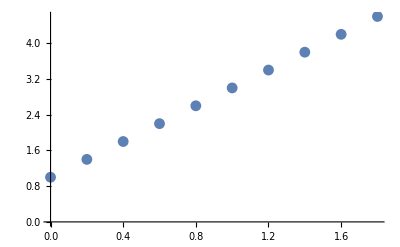

```mathematica
ListPlot[Table[{l1[[i,1]],l1[[i,2,1]]},{i,10}]]
```

```mathematica
(l2=Table[{i,{{1,i,0},{i,1,i},{0,i,1}}//Eigenvalues},{i,0,2,2/10}])//TableForm
```

0 | 1
1
1
1/5 | 1/5 (5+√2)
1
1/5 (5-√2)
2/5 | 1/5 (5+2 √2)
1
1/5 (5-2 √2)
3/5 | 1/5 (5+3 √2)
1
1/5 (5-3 √2)
4/5 | 1/5 (5+4 √2)
1
1/5 (5-4 √2)
1 | 1+√2
1
1-√2
6/5 | 1/5 (5+6 √2)
1
1/5 (5-6 √2)
7/5 | 1/5 (5+7 √2)
1
1/5 (5-7 √2)
8/5 | 1/5 (5+8 √2)
1/5 (5-8 √2)
1
9/5 | 1/5 (5+9 √2)
1/5 (5-9 √2)
1
2 | 1+2 √2
1-2 √2
1

```mathematica
Table[{l2[[i,1]],l2[[i,2,1]]},{i,10}]
```

{{0,1},{1/5,1/5 (5+√2)},{2/5,1/5 (5+2 √2)},{3/5,1/5 (5+3 √2)},{4/5,1/5 (5+4 √2)},{1,1+√2},{6/5,1/5 (5+6 √2)},{7/5,1/5 (5+7 √2)},{8/5,1/5 (5+8 √2)},{9/5,1/5 (5+9 √2)}}

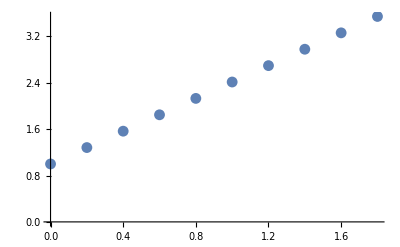

```mathematica
ListPlot[Table[{l2[[i,1]],l2[[i,2,1]]},{i,10}]]
```

```mathematica
(l3=Table[{i,{{1,i,0},{i,1,0},{0,0,1}}//Eigenvalues},{i,0,2,2/10}])//TableForm
```

0 | 1
1
1
1/5 | 6/5
1
4/5
2/5 | 7/5
1
3/5
3/5 | 8/5
1
2/5
4/5 | 9/5
1
1/5
1 | 2
1
0
6/5 | 11/5
1
-1/5
7/5 | 12/5
1
-2/5
8/5 | 13/5
1
-3/5
9/5 | 14/5
1
-4/5
2 | 3
-1
1

```mathematica
Table[{l3[[i,1]],l3[[i,2,1]]},{i,10}]
```

{{0,1},{1/5,6/5},{2/5,7/5},{3/5,8/5},{4/5,9/5},{1,2},{6/5,11/5},{7/5,12/5},{8/5,13/5},{9/5,14/5}}

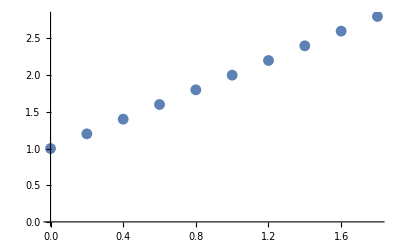

```mathematica
ListPlot[Table[{l3[[i,1]],l3[[i,2,1]]},{i,10}]]
```

```mathematica
Table[{i,{{1,i,i},{i,1,i},{i,i,1}}//Eigenvectors},{i,0,2,2/10}]//TableForm
```

0 | 0 | 0 | 1
0 | 1 | 0
1 | 0 | 0
1/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
2/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
3/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
4/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
1 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
6/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
7/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
8/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
9/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
2 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0

```mathematica
Table[{i,{{1,i,i,i},{i,1,i,i},{i,i,1,i},{i,i,i,1}}//Eigenvalues},{i,0,2,1/5}]//TableForm
```

0 | 1
1
1
1
1/5 | 8/5
4/5
4/5
4/5
2/5 | 11/5
3/5
3/5
3/5
3/5 | 14/5
2/5
2/5
2/5
4/5 | 17/5
1/5
1/5
1/5
1 | 4
0
0
0
6/5 | 23/5
-1/5
-1/5
-1/5
7/5 | 26/5
-2/5
-2/5
-2/5
8/5 | 29/5
-3/5
-3/5
-3/5
9/5 | 32/5
-4/5
-4/5
-4/5
2 | 7
-1
-1
-1

```mathematica
m={{1,0,0},{0,2,0},{0,0,3}}
```

{{1,0,0},{0,2,0},{0,0,3}}

```mathematica
Eigenvalues[m]
```

{3,2,1}

```mathematica
Eigenvectors[m]
```

{{0,0,1},{0,1,0},{1,0,0}}

```mathematica
Table[{i,e=Eigenvalues[{{1,0,0},{0,2,i},{0,i,3}}],e//Tr},{i,0,2,0.2}]//TableForm
```

0. | 3.
2.
1. | 6.
0.2 | 3.03852
1.96148
1. | 6.
0.4 | 3.14031
1.85969
1. | 6.
0.6 | 3.28102
1.71898
1. | 6.
0.8 | 3.4434
1.5566
1. | 6.
1. | 3.61803
1.38197
1. | 6.
1.2 | 3.8
1.2
1. | 6.
1.4 | 3.98661
1.01339
1. | 6.
1.6 | 4.17631
1.
0.823695 | 6.
1.8 | 4.36815
1.
0.631846 | 6.
2. | 4.56155
1.
0.438447 | 6.

```mathematica
3.0385164807134504-1.9614835192865496
```

1.07703

## Symmetric matrix

### Eigenvalues

```mathematica
(mz=(m=createRandomSymMat[10])//zeroTr)//TableForm
```

0 | 0.248134 | 0.0956967 | 0.240373 | 0.677053 | 0.656126 | 0.737405 | 0.82831 | 0.739874 | 0.766126
0.248134 | 0 | 0.574316 | 0.455944 | 0.204624 | 0.467184 | 0.945298 | 0.485438 | 0.122277 | 0.209314
0.0956967 | 0.574316 | 0 | 0.0674961 | 0.82164 | 0.279233 | 0.757785 | 0.579644 | 0.188105 | 0.040455
0.240373 | 0.455944 | 0.0674961 | 0 | 0.2444 | 0.681082 | 0.877396 | 0.0436435 | 0.531625 | 0.0318154
0.677053 | 0.204624 | 0.82164 | 0.2444 | 0 | 0.0860069 | 0.0440143 | 0.758082 | 0.831012 | 0.282224
0.656126 | 0.467184 | 0.279233 | 0.681082 | 0.0860069 | 0 | 0.809091 | 0.776618 | 0.632042 | 0.000327158
0.737405 | 0.945298 | 0.757785 | 0.877396 | 0.0440143 | 0.809091 | 0 | 0.350299 | 0.581782 | 0.292032
0.82831 | 0.485438 | 0.579644 | 0.0436435 | 0.758082 | 0.776618 | 0.350299 | 0 | 0.940422 | 0.128361
0.739874 | 0.122277 | 0.188105 | 0.531625 | 0.831012 | 0.632042 | 0.581782 | 0.940422 | 0 | 0.782158
0.766126 | 0.209314 | 0.040455 | 0.0318154 | 0.282224 | 0.000327158 | 0.292032 | 0.128361 | 0.782158 | 0

```mathematica
m//TableForm
```

0.181737 | 0.248134 | 0.0956967 | 0.240373 | 0.677053 | 0.656126 | 0.737405 | 0.82831 | 0.739874 | 0.766126
0.248134 | 0.298499 | 0.574316 | 0.455944 | 0.204624 | 0.467184 | 0.945298 | 0.485438 | 0.122277 | 0.209314
0.0956967 | 0.574316 | 0.967562 | 0.0674961 | 0.82164 | 0.279233 | 0.757785 | 0.579644 | 0.188105 | 0.040455
0.240373 | 0.455944 | 0.0674961 | 0.946202 | 0.2444 | 0.681082 | 0.877396 | 0.0436435 | 0.531625 | 0.0318154
0.677053 | 0.204624 | 0.82164 | 0.2444 | 0.460362 | 0.0860069 | 0.0440143 | 0.758082 | 0.831012 | 0.282224
0.656126 | 0.467184 | 0.279233 | 0.681082 | 0.0860069 | 0.504051 | 0.809091 | 0.776618 | 0.632042 | 0.000327158
0.737405 | 0.945298 | 0.757785 | 0.877396 | 0.0440143 | 0.809091 | 0.2495 | 0.350299 | 0.581782 | 0.292032
0.82831 | 0.485438 | 0.579644 | 0.0436435 | 0.758082 | 0.776618 | 0.350299 | 0.412108 | 0.940422 | 0.128361
0.739874 | 0.122277 | 0.188105 | 0.531625 | 0.831012 | 0.632042 | 0.581782 | 0.940422 | 0.507026 | 0.782158
0.766126 | 0.209314 | 0.040455 | 0.0318154 | 0.282224 | 0.000327158 | 0.292032 | 0.128361 | 0.782158 | 0.888375

```mathematica
v=Eigenvalues[m]
```

{4.83612,1.57894,1.31066,-1.29155,-0.786573,0.675378,-0.622519,-0.43626,0.400201,-0.248974}

```mathematica
or=Ordering[v,All,Abs[#1]>Abs[#2]&]
```

{1,2,3,4,5,6,7,8,9,10}

## Intensity Matrix

```mathematica
eigenIntensity[m]//N//MatrixForm
```

(-1.30295+0. ⅈ | -1.24103+0. ⅈ | -1.39265+0. ⅈ | -1.35134+0. ⅈ | -1.22736+0. ⅈ | -1.12119+0. ⅈ
0.196629+0. ⅈ | -0.292503+0. ⅈ | -0.336182+0. ⅈ | 0.634345+0. ⅈ | 0.379987+0. ⅈ | -0.371003+0. ⅈ
-0.246021+0.206326 ⅈ | 0.406197+0.286391 ⅈ | -0.260856-0.346898 ⅈ | 0.14452-0.158302 ⅈ | 0.0369093+0.141772 ⅈ | 0.0626156-0.0697663 ⅈ
-0.246021-0.206326 ⅈ | 0.406197-0.286391 ⅈ | -0.260856+0.346898 ⅈ | 0.14452+0.158302 ⅈ | 0.0369093-0.141772 ⅈ | 0.0626156+0.0697663 ⅈ
-0.0170972+0. ⅈ | -0.0542011+0. ⅈ | -0.171963+0. ⅈ | -0.0705667+0. ⅈ | 0.255037+0. ⅈ | 0.13231+0. ⅈ
0.0246427+0. ⅈ | -0.00073231+0. ⅈ | -0.0813538+0. ⅈ | 0.0102398+0. ⅈ | -0.0262251+0. ⅈ | 0.106004+0. ⅈ)

## 疎行列

## Memo

```mathematica
B
```

{{ⅈ,0,0},{0,ⅈ,0},{0,0,ⅈ}}

```mathematica
Bl={{I,I,0},{0,I,0},{0,0,I}}
```

{{ⅈ,ⅈ,0},{0,ⅈ,0},{0,0,ⅈ}}

```mathematica
Bc={{Normalize[I+1],0,0},{0,I,0},{0,0,I}}
```

{{(1+ⅈ)/(√2),0,0},{0,ⅈ,0},{0,0,ⅈ}}

```mathematica
Bcl={{Normalize[I+1],I,0},{0,I,0},{0,0,I}}
```

{{(1+ⅈ)/(√2),ⅈ,0},{0,ⅈ,0},{0,0,ⅈ}}

```mathematica
Eigensystem[B]
```

{{ⅈ,ⅈ,ⅈ},{{0,0,1},{0,1,0},{1,0,0}}}

```mathematica
Eigensystem[Bl]
```

{{ⅈ,ⅈ,ⅈ},{{0,0,1},{1,0,0},{0,0,0}}}

```mathematica
Eigensystem[Bc]
```

{{ⅈ,ⅈ,(1+ⅈ)/(√2)},{{0,0,1},{0,1,0},{1,0,0}}}

```mathematica
Eigensystem[Bcl]
```

{{ⅈ,ⅈ,(1+ⅈ)/(√2)},{{0,0,1},{-(1+ⅈ)/((-1-ⅈ)+√2),1,0},{1,0,0}}}

```mathematica
Norm[{-(1-ⅈ)/((-1-ⅈ)+√2),1,0}]//N
```

1.64533

```mathematica
EuclideanDistance[Normalize[2I+1],Normalize[I+2]]//N
```

0.632456

```mathematica
EuclideanDistance[Normalize[3I+1],Normalize[I+3]]//N
```

0.894427